# Notebook for: Rotating frames and measurements of forces in general relativity by De Felice

Geoff Cope
University of Utah
															𐐏𐐭𐑌𐐲𐑂𐐲𐑉𐑅𐐮𐐻𐐨 𐐲𐑂 𐐏𐐭𐐻𐐫
January 30, 2023

```mathematica
(* Very rough draft - I don't think any of these calculations are correct... come back and fix all of this *)
```

## Hyperlink To Documentation

```mathematica
Hyperlink["GeneralRelativityTensors Documentation and Download",
"https://github.com/BlackHolePerturbationToolkit"]
```

[GeneralRelativityTensors Documentation and Download](https://github.com/BlackHolePerturbationToolkit)

## Hyperlink To Book

```mathematica
Hyperlink["Rotating frames and measurements of forces in general relativity",
"https://academic.oup.com/mnras/article/252/2/197/1136736"]
```

[Rotating frames and measurements of forces in general relativity](https://academic.oup.com/mnras/article/252/2/197/1136736)

```mathematica
Hyperlink["Classical Measurements In Curved Spacetimes",
"https://www.cambridge.org/core/books/classical-measurements-in-curved-spacetimes/DAA20E1188767CB570A4A0C60BA91485"]
```

[Classical Measurements In Curved Spacetimes](https://www.cambridge.org/core/books/classical-measurements-in-curved-spacetimes/DAA20E1188767CB570A4A0C60BA91485)

## Utilities and Package Load

```mathematica
ClearAll["Global`*"]
<<Utilities`CleanSlate`
CleanSlate[]
ClearInOut[]

pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

(CleanSlate) Contexts purged: {Global`}

(CleanSlate) Approximate kernel memory recovered: 8 Kb

{Utilities`CleanSlate`,DocumentationSearch`,ResourceLocator`,NaturalLanguageProcessingLoader`,System`,Global`}

```mathematica
<<GeneralRelativityTensors`
```

## Custom Notation

```mathematica
<<Notation`
```

```mathematica
CreatePalette[{ 
PasteButton[Subscript[Ω,c]] , 
PasteButton[SubMinus[r]] ,
PasteButton[SubPlus[k]] , 
PasteButton[SubMinus[k]] 
}]
```

c4hdc_shm43FrontEndObject[LinkObject["c4hdc_shm", 3, 1]]43Untitled-6

```mathematica
Symbolize[r_+]
Symbolize[r_-]
Symbolize[r_*]
Symbolize[dr_*]
```

```mathematica
Clear[dtReplace]
dtReplace = {
Dt[p]-> dp , 
Dt[q]-> dq , 
Dt[r]-> dr , 
Dt[t]-> dt , 
Dt[v]-> dv , 
Dt[x] -> dx ,
Dt[y] -> dy ,
Dt[z]-> dz , 
Dt[λ]-> dλ , 
Dt[τ]-> dτ , 
Dt[α]-> dα ,
Dt[β]-> dβ ,  
Dt[θ]-> dθ , 
Dt[ϕ]-> dϕ , 
Dt[φ]-> dφ , 
Dt[η]-> dη , 
Dt[χ]-> dχ ,
Dt[ζ]-> dζ 
} ;
dtReplace // TableForm
```

Dt[p]→dp
Dt[q]→dq
Dt[r]→dr
Dt[t]→dt
Dt[v]→dv
Dt[x]→dx
Dt[y]→dy
Dt[z]→dz
Dt[λ]→dλ
Dt[τ]→dτ
Dt[α]→dα
Dt[β]→dβ
Dt[θ]→dθ
Dt[ϕ]→dϕ
Dt[φ]→dφ
Dt[η]→dη
Dt[χ]→dχ
Dt[ζ]→dζ

```mathematica
M/:Dt[M]=0  ; (* We use M for mass and m for null vector - otherwise recursion error *) 
Ω/:Dt[Ω]=0  ; (* Constant rotation *)
```

## Line Element and Metric Functions

```mathematica
Clear[lineToMetric]
lineToMetric[lineelement_ , differentials_]:= 
Table[If[i==j ,Coefficient[lineelement, differentials[[i]] differentials[[j]]],
(1/2)*Coefficient[lineelement, differentials[[i]] differentials[[j]]]],
{i,1,Length[differentials]},{j,1,Length[differentials]}]  ;
```

```mathematica
Clear[metricToLine]
metricToLine[metric_, differentials_]:= 
Sum[metric[[i,j]] differentials[[i]] differentials[[j]] , {i,1,Length[differentials]},{j,1,Length[differentials]}]
```

## Line Element and Metric 1: Schwarzschild

```mathematica
Clear[eq1]
eq1 = 
-(1- (2 M)/r) dt^2+(1-(2 M)/r)^-1 dr^2+ r^2( dθ^2+ Sin[θ]^2 dϕ^2)
```

dr^2/(1-(2 M)/r)+dt^2 (-1+(2 M)/r)+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric1]
metric1 = 
lineToMetric[ eq1 , {dt,dr,dθ,dϕ}]  ;
metric1// MatrixForm // pdConv
```

((2 M)/r-1 | 0 | 0 | 0
0 | 1/(1-(2 M)/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

## Calculation of Tensors For Metric 1: Schwarzschild

```mathematica
Clear[input] 
input[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList];
tensorList = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList[[2]]  = 
ChristoffelSymbol[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[3]] = 
RiemannTensor[ tensorList[[1]] , ActWithNested-> Simplify ];
tensorList[[4]] = 
RicciTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[5]] = 
RicciScalar[ tensorList[[1]] , ActWith-> Simplify ] ;
tensorList[[6]] = 
KretschmannScalar[ tensorList[[1]] , ActWith-> Simplify] ;
tensorList[[7]] = 
EinsteinTensor[ tensorList[[1]] , ActWith-> Simplify] ; 
tensorList[[8]] = 
WeylTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
 tensorList[[9]] = 
CottonTensor[ tensorList[[1]] , ActWith-> Simplify ] ;
];
```

```mathematica
(* Last timing took 2.15 for all tensors *)
input[ "metric1", metric1, "Schwarzschild","g^sch",{t,r,θ,ϕ}, "Greek"] // Timing
```

{2.97551,Null}

```mathematica
tensorList[[1]]
TensorName[tensorList[[1]]]
TensorValues[tensorList[[1]]] // MatrixForm // pdConv
```

(g^sch)_αβ^

Schwarzschild

((2 M)/r-1 | 0 | 0 | 0
0 | 1/(1-(2 M)/r) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

```mathematica
tensorList[[2]]
TensorName[tensorList[[2]]]
TensorValues[tensorList[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolSchwarzschild

((0
-M/(2 M r-r^2)
0
0) | (-M/(2 M r-r^2)
0
0
0) | (0
0
0
0) | (0
0
0
0)
((M (r-2 M))/r^3
0
0
0) | (0
M/(2 M r-r^2)
0
0) | (0
0
2 M-r
0) | (0
0
0
sin^2(θ) (2 M-r))
(0
0
0
0) | (0
0
1/r
0) | (0
1/r
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
0) | (0
0
0
1/r) | (0
0
0
cot(θ)) | (0
1/r
cot(θ)
0))

```mathematica
tensorList[[3]]
TensorName[tensorList[[3]]]
TensorValues[tensorList[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorSchwarzschild

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(2 M)/r^3 | 0 | 0
(2 M)/r^3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (M (r-2 M))/r^2 | 0
0 | 0 | 0 | 0
-(M (r-2 M))/r^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(M sin^2(θ) (2 M-r))/r^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(M sin^2(θ) (2 M-r))/r^2 | 0 | 0 | 0)
(0 | (2 M)/r^3 | 0 | 0
-(2 M)/r^3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | M/(2 M-r) | 0
0 | -M/(2 M-r) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (M sin^2(θ))/(2 M-r)
0 | 0 | 0 | 0
0 | -(M sin^2(θ))/(2 M-r) | 0 | 0)
(0 | 0 | -(M (r-2 M))/r^2 | 0
0 | 0 | 0 | 0
(M (r-2 M))/r^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -M/(2 M-r) | 0
0 | M/(2 M-r) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2 M r sin^2(θ)
0 | 0 | -2 M r sin^2(θ) | 0)
(0 | 0 | 0 | (M sin^2(θ) (2 M-r))/r^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(M sin^2(θ) (2 M-r))/r^2 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(M sin^2(θ))/(2 M-r)
0 | 0 | 0 | 0
0 | (M sin^2(θ))/(2 M-r) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -2 M r sin^2(θ)
0 | 0 | 2 M r sin^2(θ) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[4]]
TensorName[tensorList[[4]]]
TensorValues[tensorList[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorSchwarzschild

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList[[5]]
TensorName[tensorList[[5]]]
TensorValues[tensorList[[5]]] // MatrixForm // pdConv
```

R

RicciScalarSchwarzschild

0

```mathematica
tensorList[[6]]
TensorName[tensorList[[6]]]
TensorValues[tensorList[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarSchwarzschild

(48 M^2)/r^6

```mathematica
tensorList[[7]]
TensorName[tensorList[[7]]]
TensorValues[tensorList[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorSchwarzschild

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
tensorList[[8]]
TensorName[tensorList[[8]]]
TensorValues[tensorList[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorSchwarzschild

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(2 M)/r^3 | 0 | 0
(2 M)/r^3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | (M (r-2 M))/r^2 | 0
0 | 0 | 0 | 0
(M (2 M-r))/r^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | -(M sin^2(θ) (2 M-r))/r^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(M sin^2(θ) (2 M-r))/r^2 | 0 | 0 | 0)
(0 | (2 M)/r^3 | 0 | 0
-(2 M)/r^3 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | M/(2 M-r) | 0
0 | -M/(2 M-r) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (M sin^2(θ))/(2 M-r)
0 | 0 | 0 | 0
0 | -(M sin^2(θ))/(2 M-r) | 0 | 0)
(0 | 0 | (M (2 M-r))/r^2 | 0
0 | 0 | 0 | 0
(M (r-2 M))/r^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -M/(2 M-r) | 0
0 | M/(2 M-r) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2 M r sin^2(θ)
0 | 0 | -2 M r sin^2(θ) | 0)
(0 | 0 | 0 | (M sin^2(θ) (2 M-r))/r^2
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(M sin^2(θ) (2 M-r))/r^2 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(M sin^2(θ))/(2 M-r)
0 | 0 | 0 | 0
0 | (M sin^2(θ))/(2 M-r) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -2 M r sin^2(θ)
0 | 0 | 2 M r sin^2(θ) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList[[9]]
TensorName[tensorList[[9]]]
TensorValues[tensorList[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorSchwarzschild

((0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0))

## Four Velocity u and Four Acceleration for Schwarzschild (Not Finished)

```mathematica
Clear[eq2]
eq2 = 
u == Exp[ψ] {1,0,0,Ω}
```

u=={ⅇ^ψ,0,0,ⅇ^ψ Ω}

```mathematica
Clear[eq2a]
eq2a = 
Exp[ψ[r]] == ( 1 - ((2 M)/r)-Ω^2 r^2)^(-1/2)
```

ⅇ^ψ[r]==1/(√(1-(2 M)/r-r^2 Ω^2))

```mathematica
Clear[psiReplace]
psiReplace = 
Flatten[Solve[eq2a,ψ[r]]][[1]] /. C[1]-> 0  // PowerExpand
```

ψ[r]→-1/2 Log[1-(2 M)/r-r^2 Ω^2]

```mathematica
Clear[psiDerivatives]
psiDerivatives = { 
psiReplace  , 
D[psiReplace ,r] , 
D[psiReplace ,{r,2}]
}  // Expand // Simplify;
psiDerivatives  // TableForm
```

ψ[r]→-1/2 Log[1-(2 M)/r-r^2 Ω^2]
ψ'[r]→(M-r^3 Ω^2)/(2 M r-r^2+r^4 Ω^2)
ψ''[r]→(-2 M^2+2 M r-8 M r^3 Ω^2+r^4 Ω^2+r^6 Ω^4)/(r^2 (2 M-r+r^3 Ω^2)^2)

```mathematica
Clear[uComponents]
uComponents = 
eq2  /. ( eq2a /. Equal-> Rule )
```

u=={ⅇ^ψ,0,0,ⅇ^ψ Ω}

```mathematica
Clear[u]
u = ToTensor[ "u" , tensorList[[1]] , (eq2[[2]] /. ψ-> ψ[r]) , {μ}]
```

u_^μ

```mathematica
(* How on earth is this supposed to be normalized? *) 

u[μ] u[-μ]
MergeTensors[u[μ] u[-μ]]
TensorValues[MergeTensors[u[μ] u[-μ]]] // Expand // Simplify
```

u_μ^ u_^μ

(u·u)

(ⅇ^(2 ψ[r]) (2 M-r+r^3 Ω^2 Sin[θ]^2))/r

```mathematica
Denominator[eq2a[[2]]] == 0
```

√(1-(2 M)/r-r^2 Ω^2)==0

```mathematica
Clear[eq3a]
eq3a = 
Flatten[Solve[Denominator[eq2a[[2]]] == 0 ,Ω]] /. Rule-> Equal  ;
eq3a // TableForm
```

Ω==-(√(-2 M+r))/r^(3/2)
Ω==(√(-2 M+r))/r^(3/2)

```mathematica
Clear[eq3b]
eq3b = 
Flatten[Solve[Denominator[eq2a[[2]]] == 0 ,Ω]][[2]] /. Rule-> Equal
```

Ω==(√(-2 M+r))/r^(3/2)

```mathematica
Clear[eq3]
eq3 = {
Expand[ApplySides[#^2&,eq3b ] ] , 
Expand[ApplySides[#^2&,eq3b ] ] /.  Ω-> Subscript[Ω, c]
} ;
eq3 // TableForm
```

Ω^2==-(2 M)/r^3+1/r^2
Ω_c^2==-(2 M)/r^3+1/r^2

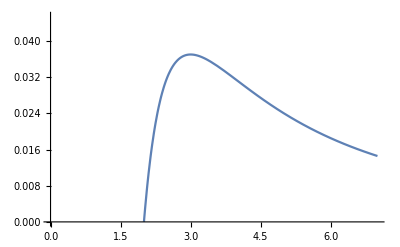

```mathematica
Clear[figure1]
figure1 = 
Plot[Evaluate[ eq3[[2]][[2]] /. M-> 1 ],{r,0,7},PlotRange->{0,1/22}]
```

```mathematica
(* figure out why this wrong... *) 

u[ν]CovariantD[u[μ],-ν]
MergeTensors[u[ν]CovariantD[u[μ],-ν]]
TensorValues[MergeTensors[u[ν]CovariantD[u[μ],-ν]]] /. psiDerivatives// Expand // Simplify
```

u_^ν (u_^α Γ_αν^μ+(∂u)_ν^μ)

(((u·u)·Γ)+(u·(∂u)))_^μ

{0,((2 M-r) (M-r^3 Ω^2 Sin[θ]^2))/(r^2 (2 M-r+r^3 Ω^2)),(r Ω^2 Cos[θ] Sin[θ])/(2 M-r+r^3 Ω^2),0}

```mathematica
TensorValues[MergeTensors[u[ν]CovariantD[u[μ],-ν]]] /. psiDerivatives /. θ-> π/2// Expand // Simplify
```

{0,((2 M-r) (M-r^3 Ω^2))/(r^2 (2 M-r+r^3 Ω^2)),0,0}

## Tetrad For Rotating Observers Given by Equation 9

```mathematica
Clear[tetrad]
tetrad = { 
λ0 ==Exp[ψ[r]]{ 1,0,0,Ω} , 
λr =={0,√(1 - (2 M)/r),0,0} , 
λθ == {0,0,1/PowerExpand[Sqrt[tensorList[[1]][-θ,-θ]]],0} , 
λϕ == {Exp[ψ[r]] (1 - (2 M)/r)^(-1/2) Ω r Sin[θ] ,0,0,(Exp[ψ[r]] √(1 - ((2 M)/r)))/(r Sin[θ])}
} ; 
tetrad // TableForm
```

λ0=={ⅇ^ψ[r],0,0,ⅇ^ψ[r] Ω}
λr=={0,√(1-(2 M)/r),0,0}
λθ=={0,0,1/r,0}
λϕ=={(ⅇ^ψ[r] r Ω Sin[θ])/(√(1-(2 M)/r)),0,0,(ⅇ^ψ[r] √(1-(2 M)/r) Csc[θ])/r}

```mathematica
Clear[λ0] (* Always check if indices are up or down and these are DOWN *) 
λ0 = 
λ0 = ToTensor[ {"NewTensor" , "λ0"} ,tensorList[[1]], tetrad[[1,2]] , {μ}]
```

λ0_^μ

```mathematica
Clear[λr] (* Always check if indices are up or down and these are DOWN *) 
λr = 
λr = ToTensor[ {"NewTensor" , "λr"} ,tensorList[[1]] , tetrad[[2,2]] , {μ}]
```

λr_^μ

```mathematica
Clear[λθ] (* Always check if indices are up or down and these are DOWN *) 
λθ = 
λθ = ToTensor[ {"NewTensor" , "λθ"} ,tensorList[[1]], tetrad[[3,2]] , {μ}]
```

λθ_^μ

```mathematica
Clear[λϕ] (* Always check if indices are up or down and these are DOWN *) 
λϕ = 
λϕ = ToTensor[ {"NewTensor" , "λϕ"} ,tensorList[[1]], tetrad[[4,2]] , {μ}]
```

λϕ_^μ

```mathematica
Clear[lambda]
lambda = 
{ λ0,λr,λθ,λϕ}
```

{λ0_^μ,λr_^μ,λθ_^μ,λϕ_^μ}

## Line Element and Metric 13: Reissner Nordstrom

```mathematica
Clear[eq13]
eq13 = 
-(1- (2 M)/r + Q^2/r^2) dt^2+(1-(2 M)/r+ Q^2/r^2)^-1 dr^2+ r^2( dθ^2+ Sin[θ]^2 dϕ^2)
```

dr^2/(1+Q^2/r^2-(2 M)/r)+dt^2 (-1-Q^2/r^2+(2 M)/r)+r^2 (dθ^2+dϕ^2 Sin[θ]^2)

```mathematica
Clear[metric13]
metric13 = 
lineToMetric[eq13,{dt,dr,dθ,dϕ}] ;
metric13 // MatrixForm // pdConv
```

((2 M)/r-Q^2/r^2-1 | 0 | 0 | 0
0 | 1/(-(2 M)/r+Q^2/r^2+1) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

## Calculation of Tensors For Metric 2: Reissner Nordstrom

```mathematica
(* $CacheTensorValues=True; *)
```

```mathematica
Clear[input2] 
input2[equationNumber_,equation_,metricName_,displayName_,variables_,indices_]:= Module[{},
Clear[tensorList2];
tensorList2 = {
"g"<>equationNumber,
"christoffel"<>equationNumber , 
"riemann"<>equationNumber  ,
"ricci"<>equationNumber ,
"ricciscalar"<>equationNumber,
"kretschmannscalar"<>equationNumber  ,
"einstein"<>equationNumber  , 
"weyl"<>equationNumber  ,
"cotton"<>equationNumber  
};
tensorList2[[1]] = 
ToMetric[{ metricName, displayName } , variables, equation, indices ] ;
tensorList2[[2]]  = 
ChristoffelSymbol[ tensorList2[[1]] , ActWith-> Simplify] ;
tensorList2[[3]] = 
RiemannTensor[ tensorList2[[1]] , ActWithNested-> Simplify ];
tensorList2[[4]] = 
RicciTensor[ tensorList2[[1]] , ActWith-> Simplify ] ;
tensorList2[[5]] = 
RicciScalar[ tensorList2[[1]] , ActWith-> Simplify ] ;
 tensorList2[[6]] = 
KretschmannScalar[ tensorList2[[1]] , ActWith-> Simplify] ; 
tensorList2[[7]] = 
EinsteinTensor[ tensorList2[[1]] , ActWith-> Simplify] ;  
tensorList2[[8]] = 
WeylTensor[ tensorList2[[1]] , ActWith-> Simplify ] ;
 tensorList2[[9]] = 
CottonTensor[ tensorList2[[1]] , ActWith-> Simplify ] ;  
];
```

```mathematica
(* Last timing took 2.55 for all tensors *)
input2[ "ReissnerNordstrom",metric13, "ReissnerNordstrom","g^kasner",{t,r,θ,ϕ}, "Greek"] // Timing
```

{3.17289,Null}

```mathematica
tensorList2
```

{(g^kasner)_αβ^,Γ_βγ^α,R_αβγδ^,R_βγ^,R,K,G_αβ^,C_αβγδ^,C_αβγ^}

```mathematica
tensorList2[[1]] 
TensorName[tensorList2[[1]]] 
TensorValues[tensorList2[[1]]] // MatrixForm // pdConv
```

(g^kasner)_αβ^

ReissnerNordstrom

((2 M)/r-Q^2/r^2-1 | 0 | 0 | 0
0 | 1/(-(2 M)/r+Q^2/r^2+1) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 sin^2(θ))

```mathematica
tensorList2[[2]] 
TensorName[tensorList2[[2]]] 
TensorValues[tensorList2[[2]]] // MatrixForm // pdConv
```

Γ_βγ^α

ChristoffelSymbolReissnerNordstrom

((0
(M r-Q^2)/(r (r (r-2 M)+Q^2))
0
0) | ((M r-Q^2)/(r (r (r-2 M)+Q^2))
0
0
0) | (0
0
0
0) | (0
0
0
0)
(((M r-Q^2) (r (r-2 M)+Q^2))/r^5
0
0
0) | (0
(Q^2-M r)/(-2 M r^2+Q^2 r+r^3)
0
0) | (0
0
2 M-(Q^2+r^2)/r
0) | (0
0
0
-(sin^2(θ) (r (r-2 M)+Q^2))/r)
(0
0
0
0) | (0
0
1/r
0) | (0
1/r
0
0) | (0
0
0
sin(θ) (-cos(θ)))
(0
0
0
0) | (0
0
0
1/r) | (0
0
0
cot(θ)) | (0
1/r
cot(θ)
0))

```mathematica
tensorList2[[3]] 
TensorName[tensorList2[[3]]] 
TensorValues[tensorList2[[3]]] // MatrixForm // pdConv
```

R_αβγδ^

RiemannTensorReissnerNordstrom

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (3 Q^2-2 M r)/r^4 | 0 | 0
-(3 Q^2-2 M r)/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | ((M r-Q^2) (r (r-2 M)+Q^2))/r^4 | 0
0 | 0 | 0 | 0
-((M r-Q^2) (r (r-2 M)+Q^2))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ) (M r-Q^2) (r (r-2 M)+Q^2))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
-(sin^2(θ) (M r-Q^2) (r (r-2 M)+Q^2))/r^4 | 0 | 0 | 0)
(0 | -(3 Q^2-2 M r)/r^4 | 0 | 0
(3 Q^2-2 M r)/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (Q^2-M r)/(-2 M r+Q^2+r^2) | 0
0 | -(Q^2-M r)/(-2 M r+Q^2+r^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (Q^2-M r))/(r (r-2 M)+Q^2)
0 | 0 | 0 | 0
0 | -(sin^2(θ) (Q^2-M r))/(r (r-2 M)+Q^2) | 0 | 0)
(0 | 0 | -((M r-Q^2) (r (r-2 M)+Q^2))/r^4 | 0
0 | 0 | 0 | 0
((M r-Q^2) (r (r-2 M)+Q^2))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | -(Q^2-M r)/(-2 M r+Q^2+r^2) | 0
0 | (Q^2-M r)/(-2 M r+Q^2+r^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (Q^2-2 M r))
0 | 0 | sin^2(θ) (Q^2-2 M r) | 0)
(0 | 0 | 0 | -(sin^2(θ) (M r-Q^2) (r (r-2 M)+Q^2))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) (M r-Q^2) (r (r-2 M)+Q^2))/r^4 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (Q^2-M r))/(r (r-2 M)+Q^2)
0 | 0 | 0 | 0
0 | (sin^2(θ) (Q^2-M r))/(r (r-2 M)+Q^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | sin^2(θ) (Q^2-2 M r)
0 | 0 | -(sin^2(θ) (Q^2-2 M r)) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList2[[4]] 
TensorName[tensorList2[[4]]] 
TensorValues[tensorList2[[4]]] // MatrixForm // pdConv
```

R_βγ^

RicciTensorReissnerNordstrom

((Q^2 (r (r-2 M)+Q^2))/r^6 | 0 | 0 | 0
0 | -Q^2/(r^2 (r (r-2 M)+Q^2)) | 0 | 0
0 | 0 | Q^2/r^2 | 0
0 | 0 | 0 | (Q^2 sin^2(θ))/r^2)

```mathematica
tensorList2[[5]] 
TensorName[tensorList2[[5]]] 
TensorValues[tensorList2[[5]]] // MatrixForm // pdConv
```

R

RicciScalarReissnerNordstrom

0

```mathematica
tensorList2[[6]] 
TensorName[tensorList2[[6]]] 
TensorValues[tensorList2[[6]]] // MatrixForm // pdConv
```

K

KretschmannScalarReissnerNordstrom

(8 (6 M^2 r^2-12 M Q^2 r+7 Q^4))/r^8

```mathematica
tensorList2[[7]] 
TensorName[tensorList2[[7]]] 
TensorValues[tensorList2[[7]]] // MatrixForm // pdConv
```

G_αβ^

EinsteinTensorReissnerNordstrom

((Q^2 (r (r-2 M)+Q^2))/r^6 | 0 | 0 | 0
0 | -Q^2/(r^2 (r (r-2 M)+Q^2)) | 0 | 0
0 | 0 | Q^2/r^2 | 0
0 | 0 | 0 | (Q^2 sin^2(θ))/r^2)

```mathematica
tensorList2[[8]] 
TensorName[tensorList2[[8]]] 
TensorValues[tensorList2[[8]]] // MatrixForm // pdConv
```

C_αβγδ^

WeylTensorReissnerNordstrom

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | (2 (Q^2-M r))/r^4 | 0 | 0
(2 (M r-Q^2))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | ((M r-Q^2) (r (r-2 M)+Q^2))/r^4 | 0
0 | 0 | 0 | 0
((Q^2-M r) (r (r-2 M)+Q^2))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | (sin^2(θ) (M r-Q^2) (r (r-2 M)+Q^2))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) (Q^2-M r) (r (r-2 M)+Q^2))/r^4 | 0 | 0 | 0)
(0 | (2 (M r-Q^2))/r^4 | 0 | 0
(2 (Q^2-M r))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (Q^2-M r)/(-2 M r+Q^2+r^2) | 0
0 | (M r-Q^2)/(r (r-2 M)+Q^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | (sin^2(θ) (Q^2-M r))/(r (r-2 M)+Q^2)
0 | 0 | 0 | 0
0 | -(sin^2(θ) (Q^2-M r))/(r (r-2 M)+Q^2) | 0 | 0)
(0 | 0 | ((Q^2-M r) (r (r-2 M)+Q^2))/r^4 | 0
0 | 0 | 0 | 0
((M r-Q^2) (r (r-2 M)+Q^2))/r^4 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | (M r-Q^2)/(r (r-2 M)+Q^2) | 0
0 | (Q^2-M r)/(-2 M r+Q^2+r^2) | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | -2 sin^2(θ) (Q^2-M r)
0 | 0 | 2 sin^2(θ) (Q^2-M r) | 0)
(0 | 0 | 0 | (sin^2(θ) (Q^2-M r) (r (r-2 M)+Q^2))/r^4
0 | 0 | 0 | 0
0 | 0 | 0 | 0
(sin^2(θ) (M r-Q^2) (r (r-2 M)+Q^2))/r^4 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | -(sin^2(θ) (Q^2-M r))/(r (r-2 M)+Q^2)
0 | 0 | 0 | 0
0 | (sin^2(θ) (Q^2-M r))/(r (r-2 M)+Q^2) | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 2 sin^2(θ) (Q^2-M r)
0 | 0 | -2 sin^2(θ) (Q^2-M r) | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
tensorList2[[9]] 
TensorName[tensorList2[[9]]] 
TensorValues[tensorList2[[9]]] // MatrixForm // pdConv
```

C_αβγ^

CottonTensorReissnerNordstrom

((0
-(4 Q^2 (r (r-2 M)+Q^2))/r^7
0
0) | ((4 Q^2 (r (r-2 M)+Q^2))/r^7
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
0) | (0
0
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
(2 Q^2)/r^3
0) | (0
-(2 Q^2)/r^3
0
0) | (0
0
0
0)
(0
0
0
0) | (0
0
0
(2 Q^2 sin^2(θ))/r^3) | (0
0
0
0) | (0
-(2 Q^2 sin^2(θ))/r^3
0
0))

## Four Velocity u and Four Acceleration a For Reissner Nordstrom

```mathematica
(* Are these the right components of the four vector *) 

Clear[𝒰]
𝒰 = ToTensor[ "𝒰" , tensorList2[[1]] , (eq2[[2]] /. ψ-> ψ[r]) , {μ}]
```

𝒰_^μ

```mathematica
(* How should this be normalized *) 

𝒰[μ]𝒰[-μ]
MergeTensors[𝒰[μ]𝒰[-μ]]
TensorValues[MergeTensors[𝒰[μ]𝒰[-μ]]]
```

𝒰_μ^ 𝒰_^μ

(𝒰·𝒰)

ⅇ^(2 ψ[r]) (-1-Q^2/r^2+(2 M)/r)+ⅇ^(2 ψ[r]) r^2 Ω^2 Sin[θ]^2

```mathematica
𝒰[μ] CovariantD[𝒰[-μ],-ν]
MergeTensors[𝒰[μ] CovariantD[𝒰[-μ],-ν]]
TensorValues[MergeTensors[𝒰[μ] CovariantD[𝒰[-μ],-ν]]] // Expand // Simplify // MatrixForm
```

𝒰_^μ (-𝒰_α^ Γ_μν^α+(∂𝒰)_νμ^)

(((-1)·((𝒰·𝒰)·Γ))+(𝒰·(∂𝒰)))_ν^

(0
(ⅇ^(2 ψ[r]) (Q^2-M r+r^4 Ω^2 Sin[θ]^2-r (Q^2-2 M r+r^2-r^4 Ω^2 Sin[θ]^2) ψ'[r]))/r^3
ⅇ^(2 ψ[r]) r^2 Ω^2 Cos[θ] Sin[θ]
0)

## Line Element and Metric 19: Internal Schwarzschild Solution

```mathematica
Clear[eq19]
eq19 = 
- ( 3/2(1-β r0^2)^(1/2) - 1/2(1-β r0^2)^(1/2))^2 dt^2+ (1-β r^2)^-1 dr^2+ r^2(dθ^2+ Sin[θ]^2)dϕ^2
```

dr^2/(1-r^2 β)+dt^2 (-1+r0^2 β)+dϕ^2 r^2 (dθ^2+Sin[θ]^2)

```mathematica
Clear[metric19]
metric19 = 
lineToMetric[eq19,{dt,dr,dθ,dϕ}]  ;
metric19// MatrixForm // pdConv
```

(β r0^2-1 | 0 | 0 | 0
0 | 1/(1-β r^2) | 0 | 0
0 | 0 | dϕ^2 r^2 | 0
0 | 0 | 0 | r^2 (dθ^2+sin^2(θ)))

```mathematica
Clear[eq19a]
eq19a = { 
β == (κ ρ0)/3 , 
κ == (8 π G)/c^4
} ;
eq19a  // TableForm
```

β==(κ ρ0)/3
κ==(8 G π)/c^4